```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pi/repos/HATS/source/tests

```mathematica
xi=ReadList["randoms.tst",Real];
```

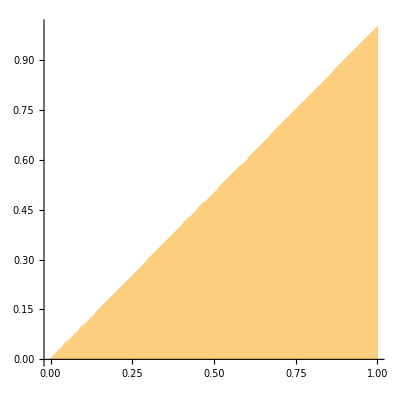

```mathematica
Histogram[xi,1000,"CDF",PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
ListPointPlot3D[Partition[xi[[1;;30000]],3],BoxRatios->1,ImageSize->Large]
```

-Graphics3D-